```mathematica
(*Алгаритм Грэхама*)
PolygonBilder[points_]:=Block[{
P = List[],
Pl = List[],Pr = List[],
Sl = List[], Sr= List[],
PlPoint , PrPoint,
length,n,
result
},
length = Length[points];
PlPoint = Part[points,1];
PrPoint =Part[points,1];

(*находим минимумальную и максимальную по иксам точку*)
For[n = 2, n ≤  length,++n,

If[Part[Part[points,n],1]<Part[PlPoint,1],PlPoint =Part[points,n]];
If[Part[Part[points,n],1]>Part[PrPoint,1],PrPoint =Part[points,n]];
];

(*делим множество на два подмножества*)
For[n = 1, n ≤  length,++n,
If[Part[points, n]== PlPoint ||Part[points, n]== PrPoint,,
If[Det[{PrPoint-PlPoint,Part[points, n]-PlPoint }]<0,AppendTo[Pr,Part[points, n]], AppendTo[Pl,Part[points, n]]]
];
];

(*вернем точки а то не хо*)
AppendTo[Pr, PlPoint];
AppendTo[Pl, PrPoint];


(*упорядочиваем*)
Pr = SortBy[Pr, First];
Pl= SortBy[Pl, First];
(*построение выпуклой оболочки для множества Pl*)
length = Length[Pl];
AppendTo[Sl, PlPoint];
For[n = 1, n ≤  length,++n,
If[Length[Sl]== 1,AppendTo[Sl,Part[Pl,n]],
If[Det[{Part[Sl, Length[Sl]]-Part[Sl, Length[Sl]-1],Part[Pl, n]-Part[Sl, Length[Sl]-1] }]≤ 0,
 AppendTo[Sl,Part[Pl,n]];,
 Sl = Delete[Sl, Length[Sl]]; n--;
];
];
];
(*построение выпуклой оболочки для множества Pr*)
length = Length[Pr];
AppendTo[Sr, PrPoint];
For[n = length,   1≤ n,--n,
If[Length[Sr]== 1,AppendTo[Sr,Part[Pr,n]],
If[Det[{Part[Sr, Length[Sr]]-Part[Sr, Length[Sr]-1],Part[Pr, n]-Part[Sr, Length[Sr]-1] }]< 0,
 AppendTo[Sr,Part[Pr,n]];,
 Sr = Delete[Sr, Length[Sr]]; n++;
];
];
];


Sr = Delete[Sr, 1];
result = Join[Sl,Sr];


Return[result]]
```

```mathematica
KickPoints[polygon_]:=Block[{
},
Return[Complement[points,polygon]]
]
```

```mathematica
Test[p1_,p2_,p3_,p4_] := Block[{
result,
α, β, k
},
α =((p2[[1]]-p1[[1]])*(p4[[1]]-p1[[1]]) +(p2[[2]]-p1[[2]])*(p4[[2]]-p1[[2]]));
β =((p2[[1]]-p3[[1]])*(p4[[1]]-p3[[1]]) +(p2[[2]]-p3[[2]])*(p4[[2]]-p3[[2]]));

If[α>0 &&β > 0, result =True,
If[α<0 &&β < 0, result =False,
k = Abs[(p2[[1]]-p1[[1]])*(p4[[2]]-p1[[2]])-(p4[[1]]-p1[[1]])*(p2[[2]]-p1[[2]])]*β 
+ α* Abs[(p2[[1]]-p3[[1]])*(p4[[2]]-p3[[2]])-(p4[[1]]-p3[[1]])*(p2[[2]]-p3[[2]])];
result = k≥0;
];
];
Return[result]
]

Flip[index_] :=Block[{
segmentN,
triangle1,triangle2,
t1i,t2i,
temp1,temp2
},

t1i =st[[index]][[1]];
t2i = st[[index]][[2]];
triangle1 = triangles[[t1i]];
triangle2 = triangles[[t2i]];

triangle1 = Complement[triangle1,{index}];
triangle2 = Complement[triangle2,{index}];

temp1 = Intersection[segments[[triangle1[[1]]]],segments[[triangle1[[2]]]]];
temp2 = Intersection[segments[[triangle2[[1]]]],segments[[triangle2[[2]]]]];

segmentN ={Flatten[temp1,1], Flatten[temp2,1]};

temp1 = triangle1;
temp2 =triangle2;
If[ Length[Intersection[segments[[triangle2[[1]]]],segments[[triangle1[[2]]]]]]== 1
,
triangle1 = {temp1[[1]],temp2[[2]],index};
triangle2 = {temp2[[1]],temp1[[2]],index};
(*Print["temp2[2].st = ",st[[temp2[[2]]]]];
Print["temp1[2].st = ",st[[temp1[[2]]]]];*)
st[[temp2[[2]]]]=Append[Complement[st[[temp2[[2]]]], {t2i}],t1i];
st[[temp1[[2]]]]=Append[Complement[st[[temp1[[2]]]], {t1i}],t2i];
,
triangle1 = {temp1[[1]],temp2[[1]],index};
triangle2 = {temp2[[2]],temp1[[2]],index};

st[[temp2[[1]]]]=Append[Complement[st[[temp2[[1]]]],{ t2i}],t1i];
st[[temp1[[2]]]]=Append[Complement[st[[temp1[[2]]]], {t1i}],t2i];
];

segments [[index]] = segmentN;
triangles[[t1i]] = triangle1;
triangles[[t2i]] = triangle2;


]
```

```mathematica
CheckStart[] := Block[{
triangle,stemp,tresult,
triangle2,triangle1,
temp1,temp2,end = False,
i,n
},
While[!end,
end = True;
For[i = 1,i ≤  Length[triangles],i++,
triangle = triangles[[i]];
For[n = 1,n ≤  Length[triangle],n++,

stemp = st[[triangle[[n]]]];
If[Length[stemp]== 2,
triangle1 = triangles[[stemp[[1]]]];
triangle2 =  triangles[[stemp[[2]]]];
triangle1 = Complement[triangle1,{triangle[[n]]}];
triangle2 = Complement[triangle2,{triangle[[n]]}];

temp1 = Intersection[segments[[triangle1[[1]]]],segments[[triangle1[[2]]]]];
temp2 = Intersection[segments[[triangle2[[1]]]],segments[[triangle2[[2]]]]];
tresult = Test[Flatten[temp1,1],segments[[triangle[[n]]]][[1]], Flatten[temp2,1],segments[[triangle[[n]]]][[2]]];
If[tresult,
(*flags[[i]] = True;*)
,
Flip[triangle[[n]]];
end =False;
];

];
];
];
];

]
```

```mathematica
SegmentIntersect[p_,q_]:= Block[{flag},
flag = !((Det[{p[[2]]-p[[1]],q[[2]]-p[[1]]}]*Det[{p[[2]]-p[[1]],q[[1]]-p[[1]]}])>0||
(Det[{q[[2]]-q[[1]],p[[2]]-q[[1]]}]*Det[{q[[2]]-q[[1]],p[[1]]-q[[1]]}])>0);
Return[flag]
]

FindMidlePoint[triangle_]:= Block[{
ab, ac,cb,
N,T,
line1,line2,
midlePoint
},
ab = segments[[triangle[[1]]]];
ac = segments[[triangle[[2]]]];
cb = segments[[triangle[[3]]]];

line1 = Intersection[ab,cb];
AppendTo[line1,(ac[[1]]+ac[[2]])/2];

line2 = Intersection[ab,ac];
AppendTo[line2,(cb[[1]]+cb[[2]])/2];

N={-Part[line2[[2]],2]+Part[line2[[1]],2],Part[line2[[2]],1]-Part[line2[[1]],1]};
T = ((line2[[1]]-line1[[1]]).N)/((line1[[2]]-line1[[1]]).N);
midlePoint = line1[[1]]*(1-T)+line1[[2]]*T;
Return[midlePoint];
]

AddPoint[point_] := Block[{
triangle,
points,
midlePoint,
line,
segment,
flag = True,
index =1,
lastIndex,
stN ,
triangle1 = {},triangle2  = {},triangle3=  {},
i
},

While[flag,
triangle = triangles[[index]];
midlePoint = FindMidlePoint[triangle];
line = {point, midlePoint};

(*Print[index];*)

segment = segments[[triangle[[1]]]];
If[SegmentIntersect[line,segment],
index =Complement[st[[triangle[[1]]]],{index}][[1]];
,

segment = segments[[triangle[[2]]]];
If[SegmentIntersect[line,segment],
index =Complement[st[[triangle[[2]]]],{index}][[1]];
,

segment = segments[[triangle[[3]]]];
If[SegmentIntersect[line,segment],
index =Complement[st[[triangle[[3]]]],{index}][[1]];
,
flag = False;
];
];
];
];
triangle = triangles[[index]];

points = Union[Flatten[{ segments[[triangle[[1]]]], segments[[triangle[[2]]]], segments[[triangle[[3]]]]},1]];
lastIndex  = Length[segments];
AppendTo[segments,{points[[1]], point}];
AppendTo[segments,{points[[2]], point}];
AppendTo[segments,{points[[3]], point}];

For[i = 1, i ≤ 3,i++,
stN = {};
(*Print[Complement[segments[[triangle[[1]]]],{points[[i]]}]];*)
(*Print[points[[i]]];*)
If[Length[Complement[segments[[triangle[[1]]]],{points[[i]]}]]== 1, AppendTo[triangle1,lastIndex +i ];AppendTo[stN,index]];
If[Length[Complement[segments[[triangle[[2]]]],{points[[i]]}]]== 1, AppendTo[triangle2,lastIndex +i ];AppendTo[stN,Length[triangles]+1]];
If[Length[Complement[segments[[triangle[[3]]]],{points[[i]]}]]== 1, AppendTo[triangle3,lastIndex +i ];AppendTo[stN,Length[triangles]+2]];
AppendTo[st,stN];
];
AppendTo[triangle1,triangle[[1]]];
AppendTo[triangle2,triangle[[2]]];
AppendTo[triangle3,triangle[[3]]];
(*
Print[triangle1];
Print[triangle2];
Print[triangle3];*)

st[[triangle[[2]]]] = Append[Complement[st[[triangle[[2]]]], {index}],Length[triangles]+1];
st[[triangle[[3]]]] = Append[Complement[st[[triangle[[3]]]], {index}],Length[triangles]+2];

triangles[[index]] = triangle1;
AppendTo[triangles,triangle2];
AppendTo[triangles, triangle3];
];

Triangulation[] := Block[{
polygon,
pointsN,
result,

i,leng,n
},
polygon = PolygonBilder[points];
polygon = Delete[polygon, Length[polygon]];
pointsN =KickPoints[polygon];

leng = Length[polygon];
For[i = 1, i < leng,i++,
AppendTo[segments,{polygon[[i]],polygon[[i+1]]}];
];
AppendTo[segments,{polygon[[leng]],polygon[[1]]}];

For[i=1, i ≤  leng, i++,
AppendTo[segments,{polygon[[i]],pointsN[[1]]}];
];

For[i=1, i <  leng, i++,
AppendTo[triangles,{i, leng+i, leng+i+1}];
];
AppendTo[triangles,{i, leng*2, leng+1}];

For[i=1, i ≤ leng, i++,
AppendTo[st,{i}];
];
AppendTo[st,{leng,1}];
For[i=2, i ≤  leng, i++,
AppendTo[st,{i-1,i}];
];

CheckStart[];

For[n = 2,  n≤ Length[pointsN],n++,
AddPoint[pointsN[[n]]];
CheckStart[];
];

Return[result]
]
```

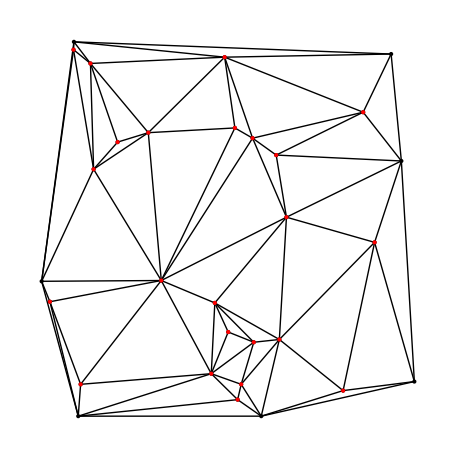

```mathematica
points= Table[{RandomInteger[{0, 1000}],RandomInteger[{0, 1000}]},{30}];
segments= List[];
triangles= List[];
st= List[];
flags= List[];
Triangulation[];
Graphics[{Line[segments], Point[points],Red, Point[KickPoints[PolygonBilder[points]]]}]
```